NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {«1»}.

NDSolve[{{{(0.+6.62607×10^-34 ⅈ) InterpolatingFunction[…][t]},{(0.+6.62607×10^-34 ⅈ) InterpolatingFunction[…][t]}}=={{2.08164×10^-33 InterpolatingFunction[…][t]+3.31304×10^-34 ⅇ^(-ⅈ Mod[(π t)/2,2 π]) Sin[theta[t]] InterpolatingFunction[…][t]},{3.31304×10^-34 ⅇ^(ⅈ Mod[(π t)/2,2 π]) Sin[theta[t]] InterpolatingFunction[…][t]-2.08164×10^-33 InterpolatingFunction[…][t]}},True,True},{InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{t,0,10}]

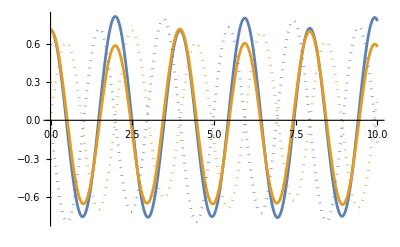

```mathematica
(*constants*)
h=6.62607015*10^-34;
w0=2 Pi;
wm=Pi/2;

(*Defining the hamiltonian*)
phi[t_]:=Mod[wm t,2 Pi]
Ω[t_]:=Sin[theta[t]]
Δ[t_]:=Cos[theta[t]]
H[t_]:=h/2 ({{w0, Ω[t] E^(-I phi[t])}, {Ω[t] E^(I phi[t]), -w0}})
(*Solve the Shrodinger equation numerically*)

NDSolve[{I h D[({{alpha[t]}, {beta[t]}}),t]==H[t].({{alpha[t]}, {beta[t]}}),alpha[0]==1/Sqrt[2],beta[0]==1/Sqrt[2]},{alpha[t],beta[t]},{t,0,10}]
(*Plot on the complex plane*)
ReImPlot[{InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{t,0,10}]
```

```mathematica
PsiVector[t_]:=({{InterpolatingFunction[…][t]}, {InterpolatingFunction[…][t]}})
```

```mathematica
alpha[t_]:=InterpolatingFunction[…][t]
beta[t_]:=InterpolatingFunction[…][t]
```

```mathematica
(*Example*)
PsiVector[5]//MatrixForm
```

```mathematica
({{-0.7388461628237506+0.07460922235019399 ⅈ}, {-0.6493012972346459-0.16415417853980788 ⅈ}})
```

{{-0.738846+0.0746092 ⅈ},{-0.649301-0.164154 ⅈ}}

```mathematica
(*The Berry phase accumulated over a complete revolution*)
```

```mathematica
PsiVector[t_]:=({{InterpolatingFunction[…][t]}, {InterpolatingFunction[…][t]}})
dPsiDt[t_]:=D[PsiVector[t],t]
berryIntegrand[t_]:=First@First@(ConjugateTranspose[PsiVector[t]].dPsiDt[t])
berryPhase=Im[Integrate[berryIntegrand[t],{t,0,2 Pi}]]*180/Pi//N
```

-170.405

```mathematica
180-170.4045160857052
```

9.59548

```mathematica
(*10 degree difference*)
```

```mathematica
(*Probabilities*)
ProbD[t_]:=Abs[PsiVector[t]]^2//FullSimplify
```

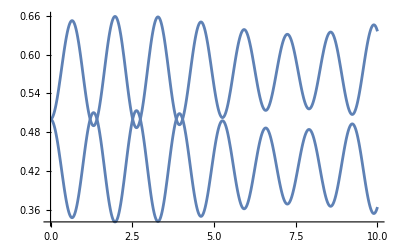

```mathematica
Plot[ProbD[t],{t,0,10}]
```

```mathematica
ProbD[10]//MatrixForm
```

(0.635885
0.364116)

```mathematica
0.6358852555212643+0.3641164234943827
```

1.

```mathematica
(*alpha + beta must be equal to 1*)
```

```mathematica
(*Bloch sphere simulation*)
```

```mathematica
(*Bloch vector from state vector*)
blochVector[t_]:=Module[{psi={alpha[t],beta[t]},sx,sy,sz},sx=2 Re[Conjugate[psi[[1]]] psi[[2]]];
sy=2 Im[Conjugate[psi[[1]]] psi[[2]]];
sz=Abs[psi[[1]]]^2-Abs[psi[[2]]]^2;
{sx,sy,sz}];

(*Path on Bloch sphere*)
blochPath=Table[blochVector[t],{t,0,10,0.05}];

(*Perpendicular vector*)
perpendicularFrame[t_]:=Module[{v=blochVector[t],u},u=Normalize[Cross[v,{0,0,1}]+0.0001 {1,0,0}];u];

Manipulate[Graphics3D[{(*Bloch Sphere*)Opacity[0.2],White,Specularity[White,20],Sphere[{0,0,0},1],(*Path on Bloch Sphere*)Thick,Orange,Line[blochPath],(*Red Arrow*)Directive[Red,Thick],Arrowheads[0.05],Arrow[{{0,0,0},blochVector[t]}],(*Blue Arrow*)Directive[Blue,Thick],Arrowheads[0.05],Arrow[{blochVector[t],blochVector[t]+0.3 perpendicularFrame[t]}]},Boxed->False,SphericalRegion->True,Axes->True,AxesLabel->{"X","Y","Z"},AxesOrigin->{0,0,0},Lighting->"Neutral",PlotRange->1.2,ImageSize->Large],{{t,0,"Time"},0,10,Animator,AnimationRate->0.2}]
```